```mathematica
(* Use Broad First Search to generate group elements from generators. *)

GenerateGroupElements[generators_]:=Module[{opn, queue={}, dim,elm,i,j, toAdd,diff, isUnique},
If[Length[generators]==0, Return[]];
dim = Length[generators[[1,1]]];
queue={IdentityMatrix[dim]};

opn = 1;
While[opn ≤ Length[queue], 
elm = queue[[opn]];
For[i=1,i≤ Length[generators],i++,
toAdd = elm.generators[[i]];
isUnique = True;
For[j=1,j≤ Length[queue],j++,
diff=Chop[N[queue[[j]]-toAdd]];
If[diff==ConstantArray[0, {dim,dim}],
isUnique = False;
Break[];
];
];

If[isUnique, 
(*Print[Simplify[toAdd]];*)
AppendTo[queue, N[toAdd]]];
];

opn = opn + 1;
];

Return[queue];
];

ClearAll[Orbit];
Options[Orbit]={AbsOnly->False};
Orbit[group_, v_,opts:OptionsPattern[]]:=Module[{i, j,res={},toAdd,diff},
For[i=1,i≤ Length[group],i++,
If[OptionValue[AbsOnly],
toAdd = Abs[group[[i]].v],
toAdd = group[[i]].v;
];

For[j=1,j≤ Length[res],j++,
diff = N[res[[j]]-toAdd];
If[Chop[diff]=={0,0,0}, Break[]];
];

If[j>Length[res], AppendTo[res, Simplify[toAdd]]]
];

Return[res]
];

ClearAll[ToNiceAngle];
SetAttributes[ToNiceAngle, Listable]
ToNiceAngle[ang_]:= Rationalize[Chop[N[ang/Pi]]]*Pi;

ClearAll[ToExp];
SetAttributes[ToExp, Listable]
ToExp[z_]:=FullSimplify[Abs[z]]*Exp[I*ToNiceAngle[Arg[z]]];

ClearAll[OutputOrbit]
OutputOrbit[absOrb_, orb_]:=Module[{cnt, phases},
Do[
cnt = 1;
phases={};
Print[absOrb[[i]]];
Do[
If[Chop[N[Abs[orb[[j]]]-absOrb[[i]]]]=={0,0,0},
AppendTo[phases, ToNiceAngle[Arg[orb[[j]]]]];
(*Print[cnt, ": ", ToExp[orb2[[j]]]];*)
cnt = cnt + 1;
],
{j,1,Length[orb]}];

phases=Sort[phases];
Print[MatrixForm[phases]];
Print["==============="],
{i,1,Length[absOrb]}];
];

Clear[Rx];Clear[Ry];Clear[Rz];
Clear[vTou];Clear[uTov];
Rx[a_]:={{1,0,0},{0,Cos[a],-Sin[a]},{0,Sin[a],Cos[a]}};
Ry[a_]:={{Cos[a],0,Sin[a]},{0,1,0},{-Sin[a],0,Cos[a]}};
Rz[a_]:={{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}};
vTou=Simplify[Rx[-Pi/4].Ry[ArcSin[1/Sqrt[3]]]];
uTov=Inverse[vTou];
```

```mathematica
Arg[{0,1,1}]
```

{0,0,0}

```mathematica
eta=Exp[2I*Pi/7];
pslgenA=I/Sqrt[7]*{
{eta^2-eta^5,eta-eta^6,eta^4-eta^3},
{eta-eta^6,eta^4-eta^3,eta^2-eta^5},
{eta^4-eta^3,eta^2-eta^5,eta-eta^6}};

pslgenB=I/Sqrt[7]*{
{eta^3-eta^6,eta^3-eta,eta-1},
{eta^2-1,eta^6-eta^5,eta^6-eta^2},
{eta^5-eta^4,eta^4-1,eta^5-eta^3}};

t7A={{0,0,1},{1,0,0},{0,1,0}};
t7B={{eta,0,0},{0,eta^2,0},{0,0,eta^4}};

ABCom=Inverse[pslgenA].Inverse[pslgenB].pslgenA.pslgenB;
AB = pslgenA.pslgenB;

Chop[N[pslgenB.pslgenB.pslgenB]];
Chop[N[pslgenA.pslgenA]];
```

```mathematica
allelm=GenerateGroupElements[{pslgenA,pslgenB}];
Length[allelm]

(*all group elements of psl27 in 6 dimensional representation. *)
allelm6=GenerateGroupElements[{OpA["6"],OpB["6"]}];
Length[allelm6]

t7allelm=GenerateGroupElements[{t7A,t7B}];
Length[t7allelm]
```

168

168

21

```mathematica
(* 
This cell verify that, in 6 representation, Conjugate[all psl27 elements] = Gamma.[all psl27 elements].Gamma. 
i.e., the conjugates of psl27 elements are the same as those obtained by similar transformation with the Gamma matrix.
But gamma is not a group memeber of psl27, so such transformation is not innermorphism. 
*)
gamma={{0,1,0},{1,0,0},{0,0,1}};
MyGamma=ArrayFlatten[{{0,gamma},{gamma,0}}];
MatrixForm[MyGamma]

OutputAllElems[elems_]:=Do[
Print[MatrixForm[Chop[elems[[3i-2]]]],MatrixForm[Chop[elems[[3i-1]]]],MatrixForm[Chop[elems[[3i]]]]],
{i,1,Length[elems]/3}];

DoubleLessThan[r1_,r2_]:=r1 + 10^-10<r2;
CLessThan[c1_,c2_]:=Module[{re,img},
If[DoubleLessThan[Re[c1],Re[c2]], Return[True]];
If[DoubleLessThan[Re[c2],Re[c1]], Return[False]];
If[DoubleLessThan[Im[c1],Im[c2]], Return[True]];
Return[False];
];

CompareComplexMatrix[mat1_,mat2_]:=Module[{len,i,j},
len = Length[mat1];
For[i=1,i≤ len, i++,
For[j=1,j≤ len, j++,
If[CLessThan[mat1[[i,j]],mat2[[i,j]]], Return[True]];
If[CLessThan[mat2[[i,j]],mat1[[i,j]]], Return[False]];
];
];

Return[False]
];

CompareElements[]:=Module[{i,j,res1={},res2,diff,dim},
Do[AppendTo[res1, MyGamma.allelm6[[i]].MyGamma],{i,1,Length[allelm6]}];
res2 = Conjugate[allelm6];
res1 =Sort[res1,CompareComplexMatrix[#1,#2] & ];
res2=Sort[res2,CompareComplexMatrix[#1,#2] & ];
dim = Length[res1[[1]]];
For[i=1,i≤ Length[res1],i++,
diff = Chop[res1[[i]] - res2[[i]]];
If[diff ≠ ConstantArray[0,{dim,dim}],
Print["diff at i=",i," mat1=",MatrixForm[Chop[res1[[i]]]], " mat2=",MatrixForm[Chop[res2[[i]]]], " diff=", MatrixForm[diff]];
 Return[False]
]
];

Return[True]
];
CompareElements[]
```

(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0)

True

```mathematica
(*OutputAllElems[allelm6]*)
```

```mathematica
orb1=Orbit[allelm, {0,0,1}, AbsOnly->True];
Length[orb1]

orb2=Orbit[allelm, {0,0,1}, AbsOnly->False];
Length[orb2]

orb3=Orbit[allelm, {1,1,1}/Sqrt[3], AbsOnly->True];
Length[orb3]

orb4=Orbit[allelm, {1,1,1}/Sqrt[3], AbsOnly->False];
Length[orb4]

p1={Sin[alpha]*Cos[beta], Sin[alpha]Sin[beta],Cos[alpha]}/.{alpha->0.1,beta->Pi/4};
p2={Sin[alpha]*Cos[beta], Sin[alpha]Sin[beta],Cos[alpha]}/.{alpha->0.2,beta->Pi/4};
p3={Sin[alpha]*Cos[beta], Sin[alpha]Sin[beta],Cos[alpha]}/.{alpha->0.3,beta->Pi/4};
orb5=Orbit[allelm, p1, AbsOnly->True];
Length[orb5]

orb6=Orbit[allelm, p1, AbsOnly->False];
Length[orb6]

orb7=Orbit[allelm, p2, AbsOnly->True];
Length[orb7]

orb8=Orbit[allelm, p2, AbsOnly->False];
Length[orb8]

orb9=Orbit[allelm, p3, AbsOnly->True];
Length[orb9]

orb10=Orbit[allelm, p3, AbsOnly->False];
Length[orb10]

t7orb1=Orbit[t7allelm, {0,0,1}, AbsOnly->True];
Length[t7orb1]
t7orb2=Orbit[t7allelm, {0,0,1}, AbsOnly->False];
Length[t7orb2]

t7orb3=Orbit[t7allelm, {1,1,1}/Sqrt[3], AbsOnly->True];
Length[t7orb3]
t7orb4=Orbit[t7allelm, {1,1,1}/Sqrt[3], AbsOnly->False];
Length[t7orb4]

(*orb1 = Sort[orb1, (Abs[N[#1[[1]]]]<Abs[N[#2[[1]]]] || Abs[N[#1[[2]]]]<Abs[N[#2[[2]]]]) &];
orb2 = Sort[orb2, (Abs[N[#1[[1]]]]<Abs[N[#2[[1]]]] || Abs[N[#1[[2]]]]<Abs[N[#2[[2]]]]) &];*)
```

6

168

4

56

15

168

15

168

15

168

3

21

1

7

```mathematica
N[ArcCos[1/Sqrt[3]]]
```

0.955317

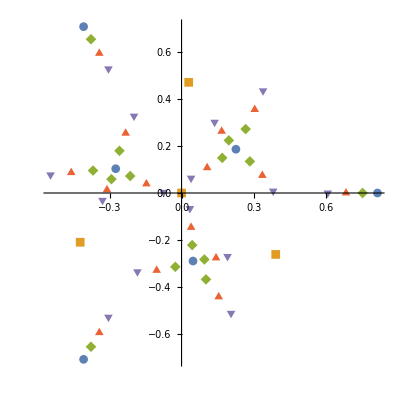

```mathematica
orb2da=Table[uTov.orb1[[i]],{i,1,Length[orb1]}];
orb2db=Table[uTov.orb3[[i]],{i,1,Length[orb3]}];
orb2dc=Table[uTov.orb5[[i]],{i,1,Length[orb5]}];
orb2dd=Table[uTov.orb7[[i]],{i,1,Length[orb7]}];
orb2de=Table[uTov.orb9[[i]],{i,1,Length[orb9]}];
ListPlot[{orb2da[[All,{1,2}]], orb2db[[All,{1,2}]],orb2dc[[All,{1,2}]],orb2dd[[All,{1,2}]],orb2de[[All,{1,2}]]},AspectRatio->1,PlotMarkers-> Automatic]
```

```mathematica
(*Do[Print[i, ": ", ToExp[orb1[[i]]]],{i,1,Length[orb1]}]*)
OutputOrbit[orb5, orb6]
```

{0.0705929,0.0705929,0.995004}

(0 | 0 | 0
-(6 π)/7 | (2 π)/7 | (4 π)/7
-(4 π)/7 | (6 π)/7 | -(2 π)/7
-(2 π)/7 | -(4 π)/7 | (6 π)/7
(2 π)/7 | (4 π)/7 | -(6 π)/7
(4 π)/7 | -(6 π)/7 | (2 π)/7
(6 π)/7 | -(2 π)/7 | -(4 π)/7)

===============

{0.2326,0.751862,0.616928}

(0 | π | π
-(6 π)/7 | -(5 π)/7 | -(3 π)/7
-(4 π)/7 | -π/7 | (5 π)/7
-(2 π)/7 | (3 π)/7 | -π/7
(2 π)/7 | -(3 π)/7 | π/7
(4 π)/7 | π/7 | -(5 π)/7
(6 π)/7 | (5 π)/7 | (3 π)/7)

===============

{0.387698,0.700871,0.598724}

(-2.85666 | 1.34002 | -3.0736
-2.52892 | 0.455178 | 0.38081
-1.95907 | 3.13521 | 0.516788
-1.63133 | 2.25037 | -2.31198
-1.06147 | -1.35278 | -2.17601
-0.733728 | -2.23762 | 1.27841
-0.16387 | 0.44242 | 1.41439
0.16387 | -0.44242 | -1.41439
0.733728 | 2.23762 | -1.27841
1.06147 | 1.35278 | 2.17601
1.63133 | -2.25037 | 2.31198
1.95907 | -3.13521 | -0.516788
2.52892 | -0.455178 | -0.38081
2.85666 | -1.34002 | 3.0736)

===============

{0.336669,0.780494,0.526766}

(-2.86828 | -3.11267 | 2.25248
-2.51731 | -1.37532 | 1.33791
-1.97068 | -1.31747 | -0.440312
-1.61971 | 0.419874 | -1.35488
-1.07308 | 0.477724 | -3.13311
-0.722115 | 2.21507 | 2.23551
-0.175483 | 2.27292 | 0.457286
0.175483 | -2.27292 | -0.457286
0.722115 | -2.21507 | -2.23551
1.07308 | -0.477724 | 3.13311
1.61971 | -0.419874 | 1.35488
1.97068 | 1.31747 | 0.440312
2.51731 | 1.37532 | -1.33791
2.86828 | 3.11267 | -2.25248)

===============

{0.712005,0.628835,0.312436}

(-3.05895 | 1.24565 | 0.839627
-2.32664 | 0.549549 | 2.75076
-2.16135 | 3.04084 | -1.85317
-1.42904 | 2.34474 | 0.057971
-1.26375 | -1.44715 | 1.73722
-0.531445 | -2.14324 | -2.63482
-0.366153 | 0.348049 | -0.955569
0.366153 | -0.348049 | 0.955569
0.531445 | 2.14324 | 2.63482
1.26375 | 1.44715 | -1.73722
1.42904 | -2.34474 | -0.057971
2.16135 | -3.04084 | 1.85317
2.32664 | -0.549549 | -2.75076
3.05895 | -1.24565 | -0.839627)

===============

{0.312436,0.712005,0.628835}

(-2.75076 | 2.32664 | -0.549549
-2.63482 | -0.531445 | -2.14324
-1.85317 | -2.16135 | 3.04084
-1.73722 | 1.26375 | 1.44715
-0.955569 | -0.366153 | 0.348049
-0.839627 | 3.05895 | -1.24565
-0.057971 | 1.42904 | -2.34474
0.057971 | -1.42904 | 2.34474
0.839627 | -3.05895 | 1.24565
0.955569 | 0.366153 | -0.348049
1.73722 | -1.26375 | -1.44715
1.85317 | 2.16135 | -3.04084
2.63482 | 0.531445 | 2.14324
2.75076 | -2.32664 | 0.549549)

===============

{0.526766,0.336669,0.780494}

(-3.13311 | -1.07308 | 0.477724
-2.25248 | 2.86828 | 3.11267
-2.23551 | 0.722115 | -2.21507
-1.35488 | -1.61971 | 0.419874
-1.33791 | 2.51731 | 1.37532
-0.457286 | 0.175483 | -2.27292
-0.440312 | -1.97068 | -1.31747
0.440312 | 1.97068 | 1.31747
0.457286 | -0.175483 | 2.27292
1.33791 | -2.51731 | -1.37532
1.35488 | 1.61971 | -0.419874
2.23551 | -0.722115 | 2.21507
2.25248 | -2.86828 | -3.11267
3.13311 | 1.07308 | -0.477724)

===============

{0.628835,0.312436,0.712005}

(-3.04084 | 1.85317 | 2.16135
-2.34474 | -0.057971 | 1.42904
-2.14324 | -2.63482 | -0.531445
-1.44715 | 1.73722 | -1.26375
-1.24565 | -0.839627 | 3.05895
-0.549549 | -2.75076 | 2.32664
-0.348049 | 0.955569 | 0.366153
0.348049 | -0.955569 | -0.366153
0.549549 | 2.75076 | -2.32664
1.24565 | 0.839627 | -3.05895
1.44715 | -1.73722 | 1.26375
2.14324 | 2.63482 | 0.531445
2.34474 | 0.057971 | -1.42904
3.04084 | -1.85317 | -2.16135)

===============

{0.780494,0.526766,0.336669}

(-3.11267 | 2.25248 | -2.86828
-2.27292 | -0.457286 | 0.175483
-2.21507 | -2.23551 | 0.722115
-1.37532 | 1.33791 | -2.51731
-1.31747 | -0.440312 | -1.97068
-0.477724 | 3.13311 | 1.07308
-0.419874 | 1.35488 | 1.61971
0.419874 | -1.35488 | -1.61971
0.477724 | -3.13311 | -1.07308
1.31747 | 0.440312 | 1.97068
1.37532 | -1.33791 | 2.51731
2.21507 | 2.23551 | -0.722115
2.27292 | 0.457286 | -0.175483
3.11267 | -2.25248 | 2.86828)

===============

{0.598724,0.387698,0.700871}

(-3.0736 | -2.85666 | 1.34002
-2.31198 | -1.63133 | 2.25037
-2.17601 | -1.06147 | -1.35278
-1.41439 | 0.16387 | -0.44242
-1.27841 | 0.733728 | 2.23762
-0.516788 | 1.95907 | -3.13521
-0.38081 | 2.52892 | -0.455178
0.38081 | -2.52892 | 0.455178
0.516788 | -1.95907 | 3.13521
1.27841 | -0.733728 | -2.23762
1.41439 | -0.16387 | 0.44242
2.17601 | 1.06147 | 1.35278
2.31198 | 1.63133 | -2.25037
3.0736 | 2.85666 | -1.34002)

===============

{0.700871,0.598724,0.387698}

(-3.13521 | -0.516788 | 1.95907
-2.25037 | 2.31198 | 1.63133
-2.23762 | 1.27841 | -0.733728
-1.35278 | -2.17601 | -1.06147
-1.34002 | 3.0736 | 2.85666
-0.455178 | -0.38081 | 2.52892
-0.44242 | -1.41439 | 0.16387
0.44242 | 1.41439 | -0.16387
0.455178 | 0.38081 | -2.52892
1.34002 | -3.0736 | -2.85666
1.35278 | 2.17601 | 1.06147
2.23762 | -1.27841 | 0.733728
2.25037 | -2.31198 | -1.63133
3.13521 | 0.516788 | -1.95907)

===============

{0.616928,0.2326,0.751862}

(-(5 π)/7 | (4 π)/7 | π/7
-(3 π)/7 | -(6 π)/7 | -(5 π)/7
-π/7 | -(2 π)/7 | (3 π)/7
π/7 | (2 π)/7 | -(3 π)/7
(3 π)/7 | (6 π)/7 | (5 π)/7
(5 π)/7 | -(4 π)/7 | -π/7
π | 0 | π)

===============

{0.751862,0.616928,0.2326}

(-(5 π)/7 | -(3 π)/7 | -(6 π)/7
-(3 π)/7 | π/7 | (2 π)/7
-π/7 | (5 π)/7 | -(4 π)/7
π/7 | -(5 π)/7 | (4 π)/7
(3 π)/7 | -π/7 | -(2 π)/7
(5 π)/7 | (3 π)/7 | (6 π)/7
π | π | 0)

===============

{0.995004,0.0705929,0.0705929}

(0 | 0 | 0
-(6 π)/7 | (2 π)/7 | (4 π)/7
-(4 π)/7 | (6 π)/7 | -(2 π)/7
-(2 π)/7 | -(4 π)/7 | (6 π)/7
(2 π)/7 | (4 π)/7 | -(6 π)/7
(4 π)/7 | -(6 π)/7 | (2 π)/7
(6 π)/7 | -(2 π)/7 | -(4 π)/7)

===============

{0.0705929,0.995004,0.0705929}

(0 | 0 | 0
-(6 π)/7 | (2 π)/7 | (4 π)/7
-(4 π)/7 | (6 π)/7 | -(2 π)/7
-(2 π)/7 | -(4 π)/7 | (6 π)/7
(2 π)/7 | (4 π)/7 | -(6 π)/7
(4 π)/7 | -(6 π)/7 | (2 π)/7
(6 π)/7 | -(2 π)/7 | -(4 π)/7)

===============

```mathematica
OutputOrbit[orb3,orb4]
```

1: {0,0,ⅇ^((4 ⅈ π)/7)}

2: {0,0,ⅇ^(-(2 ⅈ π)/7)}

3: {0,0,ⅇ^((2 ⅈ π)/7)}

4: {0,0,ⅇ^(-(6 ⅈ π)/7)}

5: {0,0,1}

6: {ⅇ^(-(2 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],-Root[1-7 #1^2+7 #1^3&,3],ⅇ^(-(3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

7: {ⅇ^((6 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^(-(3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

8: {ⅇ^(-(4 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^(-(3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

9: {ⅇ^(-(4 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^(-(5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

10: {ⅇ^((2 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^((ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

11: {ⅇ^((ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2],ⅇ^(-(6 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3]}

12: {-Root[1-7 #1^2+7 #1^3&,2],ⅇ^((2 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3]}

13: {ⅇ^((3 ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^((2 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),-2/7 (1+2 Cos[π/7]-Sin[π/14])}

14: {ⅇ^((ⅈ π)/7) √(2/7 (1+Sin[π/14])),2/7 ⅇ^(-(2 ⅈ π)/7) (-1+Cos[π/7]+2 Sin[(3 π)/14]),ⅇ^(-(ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

===============

1: {0,0,ⅇ^(-(4 ⅈ π)/7)}

2: {0,0,ⅇ^((6 ⅈ π)/7)}

3: {ⅇ^((4 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^(-(3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

4: {Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^(-(3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

5: {ⅇ^((2 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^(-(3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

6: {ⅇ^(-(4 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^((3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

7: {ⅇ^((2 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^(-(5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

8: {-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^(-(2 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^((3 ⅈ π)/7) √(2/7 (1+Cos[π/7])),2/7 ⅇ^(-(ⅈ π)/7) (1+2 Sin[π/14]+Sin[(3 π)/14])}

9: {ⅇ^(-(ⅈ π)/7) √(2/7 (1+Sin[π/14])),ⅇ^(-(2 ⅈ π)/7) √(2/7 (1-Sin[(3 π)/14])),ⅇ^((3 ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

10: {-√(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),-√(2/7 (1+Cos[π/7]))}

11: {-Root[1-7 #1^2+7 #1^3&,2],ⅇ^(-(2 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3]}

12: {ⅇ^(-(3 ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^(-(4 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^((ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

13: {ⅇ^((3 ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^((6 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^((5 ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

14: {ⅇ^((5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2],Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3]}

===============

1: {ⅇ^(-(2 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^((5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

2: {ⅇ^(-(6 ⅈ π)/7) √(2/7 (1-Sin[(3 π)/14])),ⅇ^((3 ⅈ π)/7) √(2/7 (1+Cos[π/7])),-2/7 (1+2 Sin[π/14]+Sin[(3 π)/14])}

3: {ⅇ^(-(4 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^((5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

4: {ⅇ^((4 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^((3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

5: {ⅇ^((6 ⅈ π)/7) √(2/7 (1-Sin[(3 π)/14])),ⅇ^(-(ⅈ π)/7) √(2/7 (1+Cos[π/7])),ⅇ^(-(ⅈ π)/7) √(2/7 (1+Sin[π/14]))}

6: {ⅇ^((4 ⅈ π)/7) √(2/7 (1-Sin[(3 π)/14])),ⅇ^(-(5 ⅈ π)/7) √(2/7 (1+Cos[π/7])),ⅇ^((5 ⅈ π)/7) √(2/7 (1+Sin[π/14]))}

7: {ⅇ^(-(6 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],(2 ⅇ^((ⅈ π)/7) Cos[π/14])/(√7),ⅇ^((ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

8: {ⅇ^((ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^((6 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^(-(5 ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

9: {ⅇ^(-(ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2],ⅇ^((4 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],-Root[1-7 #1^2+7 #1^3&,3]}

10: {ⅇ^(-(5 ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^((2 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^(-(5 ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

11: {ⅇ^(-(5 ⅈ π)/7) √(2/7 (1+Sin[π/14])),ⅇ^((6 ⅈ π)/7) √(2/7 (1-Sin[(3 π)/14])),-√(2/7 (1+Cos[π/7]))}

12: {2/7 ⅇ^(-(3 ⅈ π)/7) (1+2 Sin[π/14]+Sin[(3 π)/14]),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^((2 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^((5 ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

13: {ⅇ^((3 ⅈ π)/7) √(2/7 (1+Sin[π/14])),2/7 ⅇ^(-(6 ⅈ π)/7) (-1+Cos[π/7]+2 Sin[(3 π)/14]),ⅇ^(-(3 ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

14: {ⅇ^((ⅈ π)/7) √(2/7 (1+Sin[π/14])),2/7 ⅇ^((4 ⅈ π)/7) (-1+Cos[π/7]+2 Sin[(3 π)/14]),ⅇ^((3 ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

===============

1: {ⅇ^(-(2 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3],ⅇ^((3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2]}

2: {Root[-1+7 #1^2+7 #1^3&,3],-Root[1-7 #1^2+7 #1^3&,3],-Root[1-7 #1^2+7 #1^3&,2]}

3: {ⅇ^((3 ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^(-(4 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^((3 ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

4: {ⅇ^((3 ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^((ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

5: {ⅇ^((3 ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^(-(2 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^(-(5 ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

6: {ⅇ^(-(3 ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^(-(2 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),-2/7 (1+2 Cos[π/7]-Sin[π/14])}

7: {ⅇ^(-(3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2],ⅇ^((6 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3]}

8: {-Root[1-7 #1^2+7 #1^3&,2],ⅇ^(-(6 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3]}

9: {ⅇ^((5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2],ⅇ^((2 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((3 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3]}

10: {-Root[1-7 #1^2+7 #1^3&,2],ⅇ^(-(4 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3]}

11: {ⅇ^(-(5 ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^(-(2 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^(-(3 ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

12: {ⅇ^(-(5 ⅈ π)/7) √(2/7 (1+Sin[π/14])),-1/7 (-1)^(6/7) (1+(-1)^(1/7))^2 ⅇ^(-(6 ⅈ π)/7) √(17-24 Cos[π/7]+8 Sin[(3 π)/14]),ⅇ^(-(ⅈ π)/7) √(2/7 (1+Cos[π/7]))}

13: {ⅇ^(-(ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2],Root[-1+7 #1^2+7 #1^3&,3],ⅇ^(-(5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3]}

14: {ⅇ^((5 ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,2],ⅇ^((6 ⅈ π)/7) Root[-1+7 #1^2+7 #1^3&,3],ⅇ^((ⅈ π)/7) Root[1-7 #1^2+7 #1^3&,3]}

===============